# FileAdapterGSDGSH test

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

(last updated:  Fri 28 Feb 2014 10:56:28)

<<Set JLink` java stack size to 3072Mb>>

```mathematica
ShowJavaConsole[];
```

```mathematica
testDataFile = "V:\\docs\\bb\\nounous\\src\\test\\resources\\_testFiles\\Micam\\mag130712008A_3.gsd";
```

```mathematica
$NNReader@load[testDataFile]
```

```mathematica
$NNReader@toStringChain[]
```

DataReader LOADED DATA SUMMARY
================================
DataReader( data ch:7360, dataAux ch:2, mask: XMask: 0 _masks, events: 0)

     [header  ] XHeader: 26 entries
     [dataORI ] XDataFilterHolder: XData: 7360 ch, 1 seg, lengths=Vector(1024), fs=500.0)     
          \ XDataFilterDecimate: off (factor=1)     
               \ XDataFilterBuffer: bufferPageLength=16384, garbageQueBound=1024     
                    \ XDataFilterStatistics: 
                    \ XDataFilterMinMaxAbs: halfWindow=25
                    \ XDataFilterFIR: kernel null (off)
                    \ XDataFilterFIR: kernel null (off)     
                         \ XDataFilterRMS: halfWindow=25
     [dataAux ] XDataFilterHolder: XData: 2 ch, 1 seg, lengths=Vector(1024), fs=500.0)
     [mask    ] XMask: 0 _masks
     [events  ] XEventsNull
     [spikes  ] XSpikesNull

```mathematica
$NNReader@dataFIR[]@segmentLengths[]@toString[]
```

Vector(1024)

```mathematica
$NNReader@dataDecimate[]@segmentLengths[]@toString[]
```

Vector(1024)

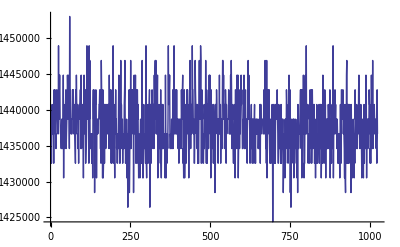

```mathematica
ListLinePlot[$NNReader@dataFIR[]@readTraceAbsA[100, NN`frameRangeAll[]]]
```

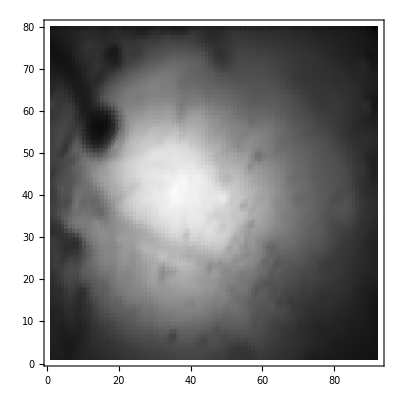

```mathematica
ListDensityPlot[Partition[$NNReader@dataFIR[]@readFrameA[0,0],92],ColorFunction->GrayLevel]
```

```mathematica
$NNReader@dataORI[]@heldDataU$eq[]
```

Java::argx0: Method named "heldDataU$eq" defined in class "nounou.data.filters.XDataFilterHolder" does not take zero arguments.

$Failed

```mathematica
Methods[$NNReader@dataORI[]]
```